Negative energies

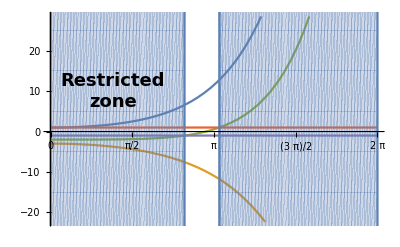

```mathematica
α=Rationalize[3];
rmax = 2*π;
equation = Cosh[x]-α*Sinh[x]/x;
p1 = Plot[{Cosh[x],-α*Sinh[x]/x, equation, 1, -1}, {x, 0, rmax},Ticks->{Range[0,rmax,Pi/2],Automatic}, ImageSize->Full];
regions = Reduce[Abs[equation] ≥  1&&0<x<rmax,x];
p2=RegionPlot[N[regions, 10], {x, 0, rmax}, {y, -500, 500}, PlotPoints->100];
text=Graphics[{Text[Style["Restricted\nzone",Bold,18],{1.2,10}]}];
Show[p1, p2, text]
```

Positive energies

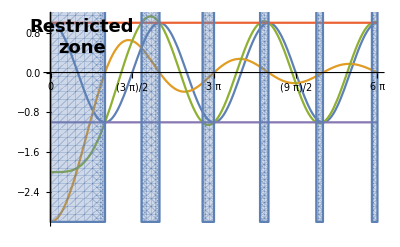

```mathematica
α=3;
rmax = 6*π;
equation = Cos[x]-α*Sin[x]/x;
p1 = Plot[{Cos[x],-α*Sin[x]/x, equation, 1, -1}, {x, 0, rmax},Ticks->{Range[0,rmax,Pi/2],Automatic}, ImageSize->Full];
regions = Reduce[Abs[equation] ≥  1&&0<x<rmax,x];
p2=RegionPlot[N[regions, 10], {x, 0, rmax}, {y, -3, 3}, PlotPoints->40];
text=Graphics[{Text[Style["Restricted\nzone",Bold,18],{1.8,0.7}]}];
Show[p1, p2, text]
```

E(K) plots

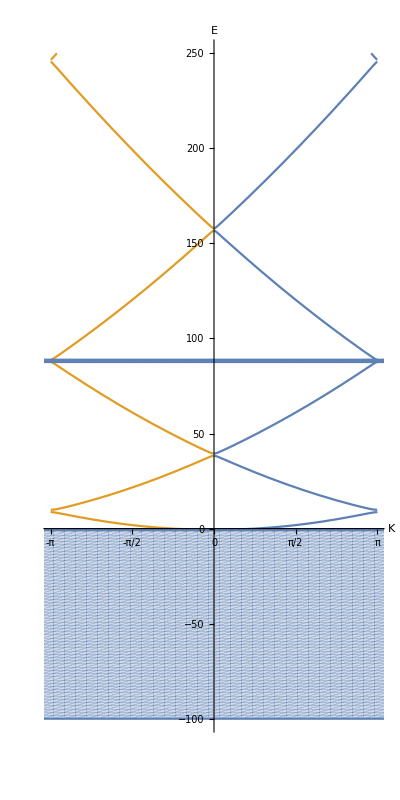

```mathematica
α=Rationalize[0.3];
posrmax = Sqrt[250];
negrmax =10;
equation = Cos[x]-α*Sin[x]/x;
func[x_]:=ArcCos[equation];
positive = Quiet[ParametricPlot[{{func[x], x^2},{-func[x],x^2}}, {x, 0, posrmax}, AspectRatio->2, ImageSize->400, Ticks->{Range[-π,π,Pi/4],Automatic},PlotRange->{{-π,π},{-negrmax^2,posrmax^2}}, AxesLabel->{"K","E"}]];
regions = Reduce[Abs[equation/.x->Sqrt[y]] ≥  1&&0<y<posrmax^2,y];
positivezones = RegionPlot[regions,{x, -2*π, 2*π}, {y, 0, posrmax^2}, PlotPoints->100];
equation = Cosh[x]-α*Sinh[x]/x;
func[x_]:=ArcCos[equation];
negative = Quiet[ParametricPlot[{{func[x], -x^2},{-func[x],-x^2}}, {x, 0, negrmax}]];
regions = Reduce[Abs[equation/.x->Sqrt[-y]] ≥  1&&-negrmax^2<y<0,y];
negativezones = RegionPlot[regions,{x, -2*π, 2*π}, {y, -negrmax^2, 0}, PlotPoints->60];
plot=Show[positive, negative, positivezones, negativezones]
```

```mathematica
Monitor[
plots2=Table[
α=a;
posrmax = Sqrt[250];
negrmax =10;
equation = Cos[x]-α*Sin[x]/x;
func[x_]:=ArcCos[equation];
positive = Quiet[ParametricPlot[{{func[x], x^2},{-func[x],x^2}}, {x, 0, posrmax}, AspectRatio->2, ImageSize->400, Ticks->{Range[-π,π,Pi/4],Automatic},PlotRange->{{-π,π},{-negrmax^2,posrmax^2}}, AxesLabel->{"K","E"}]];
regions = Reduce[Abs[equation/.x->Sqrt[y]] ≥  1&&0<y<posrmax^2,y];
positivezones = RegionPlot[regions,{x, -2*π, 2*π}, {y, 0, posrmax^2}, PlotPoints->100];
equation = Cosh[x]-α*Sinh[x]/x;
func[x_]:=ArcCos[equation];
negative = Quiet[ParametricPlot[{{func[x], -x^2},{-func[x],-x^2}}, {x, 0, negrmax}]];
regions = Reduce[Abs[equation/.x->Sqrt[-y]] ≥  1&&-negrmax^2<y<0,y];
negativezones = RegionPlot[regions,{x, -2*π, 2*π}, {y, -negrmax^2, 0}, PlotPoints->60];
Show[positive, negative, positivezones, negativezones], {a, Round[100*PowerRange[1, 1000, 1.1]]/1000}];,
Row[{ProgressIndicator[a,{0.1, 100}],a}," "]
]
```

```mathematica
Export["/Users/smart/Desktop/10.gif", plots2]
```

/Users/smart/Desktop/10.gif

```mathematica
Export["10.gif"ListAnimate[plots2]
```

```mathematica
Round[100*PowerRange[1, 1000, 1.1]]/1000
```

{1/10,11/100,121/1000,133/1000,73/500,161/1000,177/1000,39/200,107/500,59/250,259/1000,57/200,157/500,69/200,19/50,209/500,459/1000,101/200,139/250,153/250,673/1000,37/50,407/500,179/200,197/200,1083/1000,149/125,1311/1000,721/500,793/500,349/200,1919/1000,2111/1000,2323/1000,511/200,281/100,3091/1000,17/5,187/50,2057/500,2263/500,4979/1000,1369/250,753/125,3313/500,7289/1000,4009/500,441/50,4851/500,1334/125,11739/1000,12913/1000,3551/250,125/8,17187/1000,9453/500,20797/1000,5719/250,6291/250,692/25,3806/125,33493/1000,18421/500,40527/1000,44579/1000,49037/1000,53941/1000,11867/200,16317/250,14359/200,3159/40,10859/125,95559/1000}

```mathematica
"3.2"×10^("-2"),"4.1"×10^("-2")
```

```mathematica
NumberForm[8534.564564566,2]
```

NumberForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

8500.

```mathematica
ScientificForm[4.5]
```

4.5